```mathematica
Public assessment of reputations
```

```mathematica
Global Conditions
```

Conditions Global

```mathematica
Clear["Global`*"]
r=1.5;
ϵ=(1-e1)*(1-e)+e1*e;
SetDirectory["/Users/brycemorsky/Desktop/New projects/Indirect reciprocity/figures"];
```

```mathematica
Scoring
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
Pcg=ϵ*g/(ϵ*g+e*(1-g));
Pdg=(1-ϵ)*g/((1-ϵ)*g+(1-e)*(1-g));
Pcb=Pcg;
Pdb=Pdg;
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
Qcb=ϵ*Pcb+(1-ϵ)*Pdb;
Qdb=(1-e)*Pdb+e*Pcb;
repsys={
gx'[t]==Qcg-gx[t],
gy'[t]==Qdg-gy[t],
gz'[t]==(Qcg*g+Qdg*(1-g))-gz[t]
};
M=Array[m,{66,5}];
count=1;
Do[
R=NDSolve[Join[repsys/.{x->0.1*i,y->0.1*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{gx,gy,gz},{t,0,100}];
M[[count]]= {0.1*i,0.1*j,gx[100]/.R[[1]],gy[100]/.R[[1]],gz[100]/.R[[1]]};
count=count+1;
,{i,0,10},{j,0,10-i}];
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);

(* Stable equilibria *)
fullsys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100*(Qcg-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(100*(Qdg-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(100*(Qcg*g+Qdg*(1-g)-gz[t])/.{x->x[t],y->y[t]})
};
Eqstable=Array[m,{81,2}];
count = 1;
Do[
R=NDSolve[Join[fullsys,{x[0]==0.00402*i,y[0]==0.00402*i,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{x,y,gx,gy,gz},{t,0,100000},Method->"StiffnessSwitching"];
Eqstable[[count]]= {x[100000]/.R[[1]],y[100000]/.R[[1]]};
count=count+1;
,{i,0,80}];
(* Unstable equilibria *)
fullsys={
x'[t]==-(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==-(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100*(Qcg-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(100*(Qdg-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(100*(Qcg*g+Qdg*(1-g)-gz[t])/.{x->x[t],y->y[t]})
};
Equnstable=Array[m,{81,2}];
count = 1;
Do[
R=NDSolve[Join[fullsys,{x[0]==0.00402*i,y[0]==0.00402*i,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{x,y,gx,gy,gz},{t,0,100000},Method->"StiffnessSwitching"];
Equnstable[[count]]= {x[100000]/.R[[1]],y[100000]/.R[[1]]};
count=count+1;
,{i,0,80}];

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],Thickness[diskradius+thickness*2],EdgeForm[Blue],Blue,Line[TernCoords[#1,#2]&@@@{{0,1},{0,0.66}}]}],
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],Thickness[diskradius+thickness*2],EdgeForm[Blue],Blue,Line[TernCoords[#1,#2]&@@@{{0,0},{0,0.66}}]}],
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],Thickness[diskradius],EdgeForm[Blue],White,Line[TernCoords[#1,#2]&@@@{{0,0},{0,0.66}}]}],
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],Thickness[diskradius+thickness*2],EdgeForm[Blue],Blue,Line[TernCoords[#1,#2]&@@@{{0,1},{0,0}}]}],
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],Thickness[diskradius+thickness*2],EdgeForm[Blue],Blue,Line[TernCoords[#1,#2]&@@@Join[Eqstable,{{0.32295466114708093,0.32295466114708093}}]]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0.32295466114708093,0.32295466114708093],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],Dashing[0.04],CapForm["Round"],Thickness[diskradius],EdgeForm[Blue],Red,Line[TernCoords[#1,#2]&@@@Join[Equnstable,{{0.32295466114708093,0.32295466114708093}}]]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0.32295466114708093,0.32295466114708093],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,0],diskradius]}]
};

dp=ListStreamPlot[Partition[#,2]&/@vdata,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageScBayes=Show[ternplot,dots,vlabels, ImageSize->Large,PlotRangePadding->.1];;
Export["Sc.pdf",imageScBayes];
```

Scoring

Simple Standing

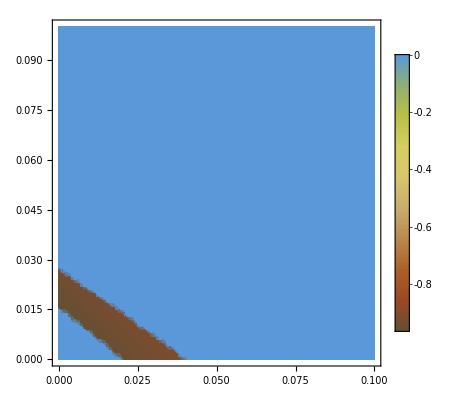

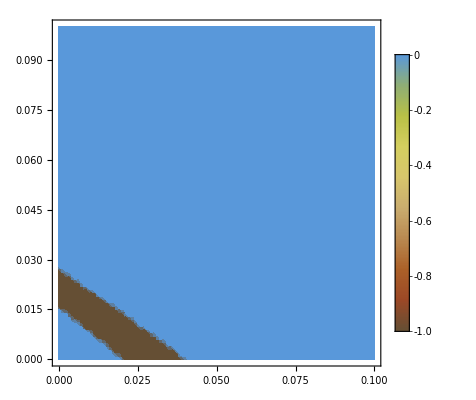

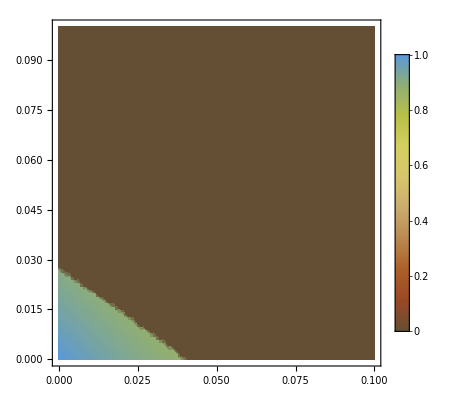

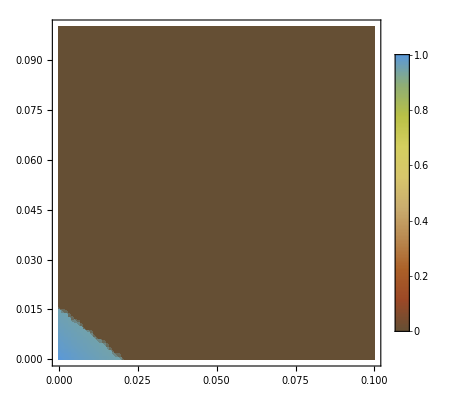

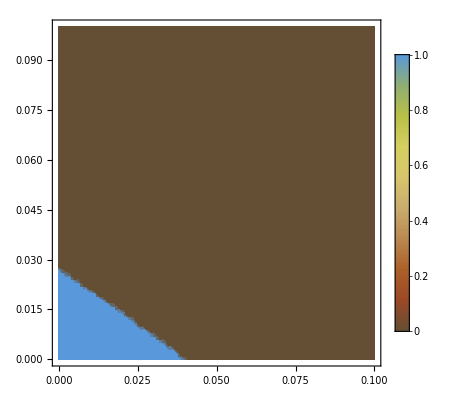

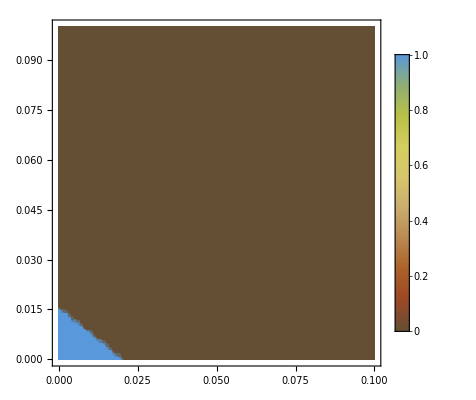

```mathematica
Simple Standing
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx2[t]+y*gy2[t]+(1-x-y)*gz2[t];
gb=g*0.95;
Pcg=ϵ*gb/(ϵ*gb+e*(1-gb));
Pdg=(1-ϵ)*gb/((1-ϵ)*gb+(1-e)*(1-gb));
Pcb=1;
Pdb=1;
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
Qcb=ϵ*Pcb+(1-ϵ)*Pdb;
Qdb=(1-e)*Pdb+e*Pcb;
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
(* Stable equilibria *)
Bayessys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*(Qcg*g+1-g-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(10000*(Qdg*g+1-g-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(10000*(Qcg*g2+Qdg*(g-g2)+1-g-gz[t])/.{x->x[t],y->y[t]}),
gx2'[t]==(10000*(gx[t]^2-gx2[t])/.{x->x[t],y->y[t]}),
gy2'[t]==(10000*(gy[t]^2-gy2[t])/.{x->x[t],y->y[t]}),
gz2'[t]==(10000*(gz[t]^2-gz2[t])/.{x->x[t],y->y[t]})
};
nonBayessys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*(ϵ*g+(1-e)*(1-g)-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(10000*(e*g+(1-e)*(1-g)-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(10000*(ϵ*g2+e*(g-g2)+(1-e)*(1-g)-gz[t])/.{x->x[t],y->y[t]}),
gx2'[t]==(10000*(gx[t]^2-gx2[t])/.{x->x[t],y->y[t]}),
gy2'[t]==(10000*(gy[t]^2-gy2[t])/.{x->x[t],y->y[t]}),
gz2'[t]==(10000*(gz[t]^2-gz2[t])/.{x->x[t],y->y[t]})
};
coopBayes=Array[m,{10201,3}];
zoutBayes=Array[m,{10201,3}];
coopnonBayes=Array[m,{10201,3}];
zoutnonBayes=Array[m,{10201,3}];
coop=Array[m,{10201,3}];
zout=Array[m,{10201,3}];
count = 1;
Do[
RBayes=NDSolve[Join[Evaluate[Bayessys/.{e1->i/1000,e->j/1000}],{x[0]==0.1,y[0]==0.1,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.5,gy2[0]==0.5,gz2[0]==0.5}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,100000},Method->"StiffnessSwitching"];
RnonBayes=NDSolve[Join[Evaluate[nonBayessys/.{e1->i/1000,e->j/1000}],{x[0]==0.1,y[0]==0.1,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.5,gy2[0]==0.5,gz2[0]==0.5}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,100000},Method->"StiffnessSwitching"];
coopBayes[[count]]= {i/1000,j/1000,(1-y[100000])*(gy[100000]*y[100000]+gz[100000]*(1-y[100000]))/.RBayes[[1]]};
zoutBayes[[count]]= {i/1000,j/1000,1-y[100000]/.RBayes[[1]]};
coopnonBayes[[count]]= {i/1000,j/1000,(1-y[100000])*(gy[100000]*y[100000]+gz[100000]*(1-y[100000]))/.RnonBayes[[1]]};
zoutnonBayes[[count]]= {i/1000,j/1000,1-y[100000]/.RnonBayes[[1]]};
coop[[count]]= {i/1000,j/1000,Evaluate[x[100000]+(1-x[100000]-y[100000])*(gx[100000]*x[100000]+gy[100000]*y[100000]+gz[100000]*(1-x[100000]-y[100000]))/.RBayes[[1]]]-Evaluate[x[100000]+(1-x[100000]-y[100000])*(gx[100000]*x[100000]+gy[100000]*y[100000]+gz[100000]*(1-x[100000]-y[100000]))/.RnonBayes[[1]]]};
zout[[count]]= {i/1000,j/1000,Evaluate[1-y[100000]/.RBayes[[1]]]-Evaluate[1-y[100000]/.RnonBayes[[1]]]};
count=count+1;
,{i,0,100},{j,0,100}];
ListDensityPlot[coop,ColorFunction->"SouthwestColors",PlotRange->Full,PlotLegends->Automatic]
ListDensityPlot[zout,ColorFunction->"SouthwestColors",PlotRange->Full,PlotLegends->Automatic]
ListDensityPlot[coopnonBayes,ColorFunction->"SouthwestColors",PlotRange->Full,PlotLegends->Automatic]
ListDensityPlot[coopBayes,ColorFunction->"SouthwestColors",PlotRange->Full,PlotLegends->Automatic]
ListDensityPlot[zoutnonBayes,ColorFunction->"SouthwestColors",PlotRange->Full,PlotLegends->Automatic]
ListDensityPlot[zoutBayes,ColorFunction->"SouthwestColors",PlotRange->Full,PlotLegends->Automatic]
```

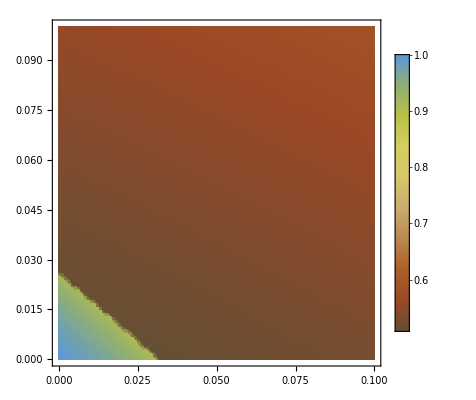

```mathematica
ListDensityPlot[coop,ColorFunction->"SouthwestColors",PlotRange->Full,PlotLegends->Automatic]
```

Staying

General::munfl: -6.37713×10^-295 (-5.19198×10^-73) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -1.82933×10^-298 9.90273×10^-73 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

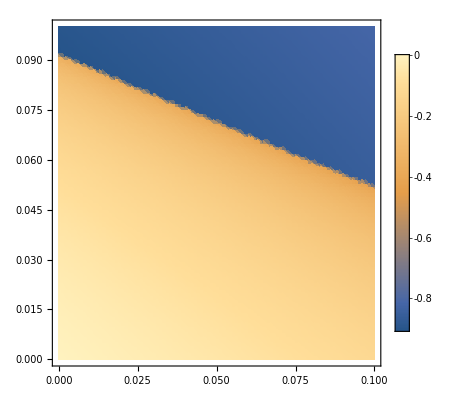

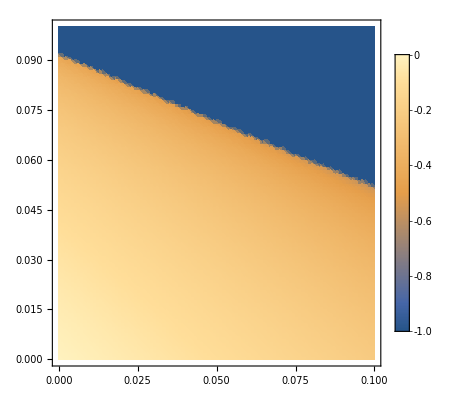

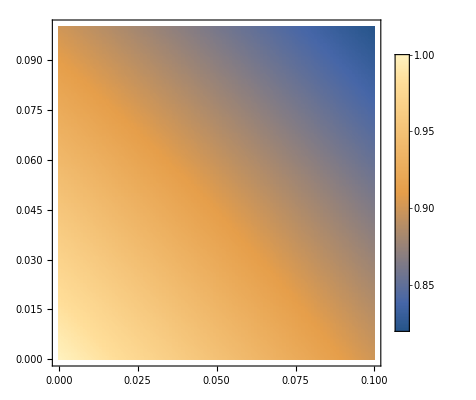

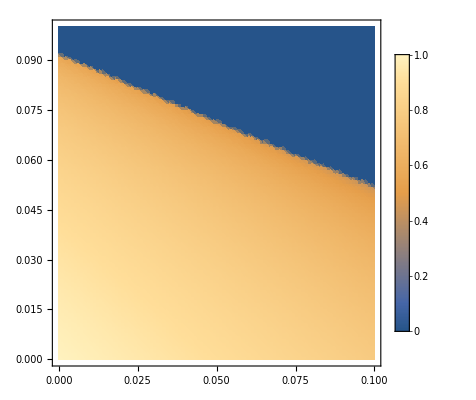

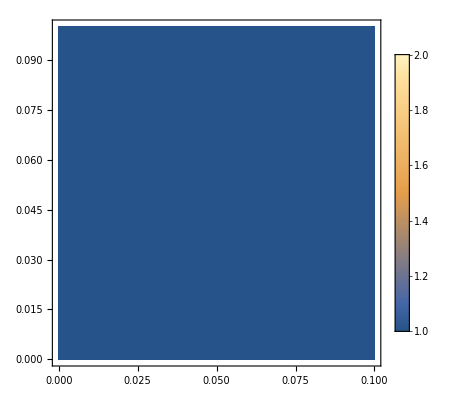

-Graphics-

```mathematica
Staying
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx2[t]+y*gy2[t]+(1-x-y)*gz2[t];
Pcg=ϵ*g/(ϵ*g+e*(1-g));
Pdg=(1-ϵ)*g/((1-ϵ)*g+(1-e)*(1-g));
Pcb=e*g/(e*g+ϵ*(1-g));
Pdb=(1-e)*g/((1-e)*g+(1-ϵ)*(1-g));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
Qcb=ϵ*Pcb+(1-ϵ)*Pdb;
Qdb=(1-e)*Pdb+e*Pcb;
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
(* Stable equilibria *)
Bayessys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100*(Qcg-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(100*(Qdg-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(100*(Qcg-gz[t])/.{x->x[t],y->y[t]})
};
nonBayessys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100*(ϵ-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(100*(e-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(100*(ϵ-gz[t])/.{x->x[t],y->y[t]})
};
coopBayes=Array[m,{10201,3}];
zoutBayes=Array[m,{10201,3}];
coopnonBayes=Array[m,{10201,3}];
zoutnonBayes=Array[m,{10201,3}];
coop=Array[m,{10201,3}];
zout=Array[m,{10201,3}];
count = 1;
Do[
RBayes=NDSolve[Join[Evaluate[Bayessys/.{e1->i/1000,e->j/1000}],{x[0]==0.1,y[0]==0.1,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{x,y,gx,gy,gz},{t,0,100000},Method->"StiffnessSwitching"];
RnonBayes=NDSolve[Join[Evaluate[nonBayessys/.{e1->i/1000,e->j/1000}],{x[0]==0.1,y[0]==0.1,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{x,y,gx,gy,gz},{t,0,100000},Method->"StiffnessSwitching"];
coopBayes[[count]]= {i/1000,j/1000,gy[100000]*y[100000]+gz[100000]*(1-y[100000])/.RBayes[[1]]};
zoutBayes[[count]]= {i/1000,j/1000,1-y[100000]/.RBayes[[1]]};
coopnonBayes[[count]]= {i/1000,j/1000,gy[100000]*y[100000]+gz[100000]*(1-y[100000])/.RnonBayes[[1]]};
zoutnonBayes[[count]]= {i/1000,j/1000,1-y[100000]/.RnonBayes[[1]]};
coop[[count]]= {i/1000,j/1000,Evaluate[gy[100000]*y[100000]+gz[100000]*(1-y[100000])/.RBayes[[1]]]-Evaluate[gy[100000]*y[100000]+gz[100000]*(1-y[100000])/.RnonBayes[[1]]]};
zout[[count]]= {i/1000,j/1000,Evaluate[1-y[100000]/.RBayes[[1]]]-Evaluate[1-y[100000]/.RnonBayes[[1]]]};
count=count+1;
,{i,0,100},{j,0,100}];
ListDensityPlot[coop,PlotRange->Full,PlotLegends->Automatic]
ListDensityPlot[zout,PlotRange->Full,PlotLegends->Automatic]
ListDensityPlot[coopnonBayes,PlotRange->Full,PlotLegends->Automatic]
ListDensityPlot[coopBayes,PlotRange->Full,PlotLegends->Automatic]
ListDensityPlot[zoutnonBayes,PlotRange->Full,PlotLegends->Automatic]
ListDensityPlot[zoutBayes,PlotRange->Full,PlotLegends->Automatic]
```

judging Stern

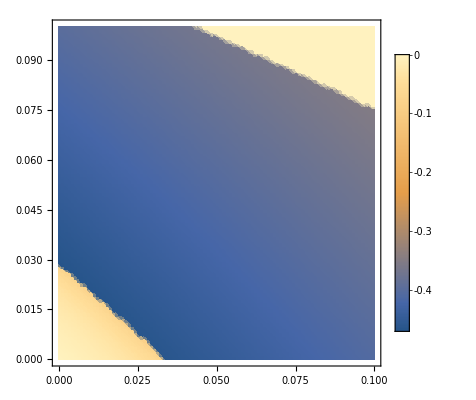

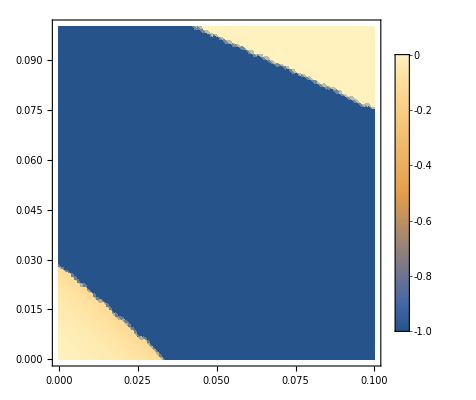

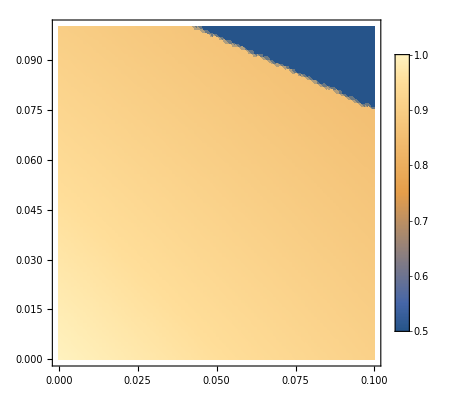

-Graphics-

-Graphics-

-Graphics-

```mathematica
Stern judging
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx2[t]+y*gy2[t]+(1-x-y)*gz2[t];
Pcg=ϵ*g/(ϵ*g+e*(1-g));
Pdg=(1-ϵ)*g/((1-ϵ)*g+(1-e)*(1-g));
Pcb=e*g/(e*g+ϵ*(1-g));
Pdb=(1-e)*g/((1-e)*g+(1-ϵ)*(1-g));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
Qcb=ϵ*Pcb+(1-ϵ)*Pdb;
Qdb=(1-e)*Pdb+e*Pcb;
repsys={
gx'[t]==Qcg*g+Qcb*(1-g)-gx[t],
gy'[t]==Qdg*g+Qdb*(1-g)-gy[t],
gz'[t]==Qcg*g+Qdb*(1-g)-gz[t]
};
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
(* Stable equilibria *)
Bayessys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100*(Qcg*g+Qcb*(1-g)-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(100*(Qdg*g+Qdb*(1-g)-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(100*(Qcg*g+Qdb*(1-g)-gz[t])/.{x->x[t],y->y[t]})
};
nonBayessys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100*(ϵ*g+(1-ϵ)*(1-g)-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(100*(e*g+(1-e)*(1-g)-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(100*(ϵ*g+(1-e)*(1-g)-gz[t])/.{x->x[t],y->y[t]})
};
coopBayes=Array[m,{10201,3}];
zoutBayes=Array[m,{10201,3}];
coopnonBayes=Array[m,{10201,3}];
zoutnonBayes=Array[m,{10201,3}];
coop=Array[m,{10201,3}];
zout=Array[m,{10201,3}];
count = 1;
Do[
RBayes=NDSolve[Join[Evaluate[Bayessys/.{e1->i/1000,e->j/1000}],{x[0]==0.1,y[0]==0.1,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{x,y,gx,gy,gz},{t,0,100000},Method->"StiffnessSwitching"];
RnonBayes=NDSolve[Join[Evaluate[nonBayessys/.{e1->i/1000,e->j/1000}],{x[0]==0.1,y[0]==0.1,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{x,y,gx,gy,gz},{t,0,100000},Method->"StiffnessSwitching"];
coopBayes[[count]]= {i/1000,j/1000,gy[100000]*y[100000]+gz[100000]*(1-y[100000])/.RBayes[[1]]};
zoutBayes[[count]]= {i/1000,j/1000,1-y[100000]/.RBayes[[1]]};
coopnonBayes[[count]]= {i/1000,j/1000,gy[100000]*y[100000]+gz[100000]*(1-y[100000])/.RnonBayes[[1]]};
zoutnonBayes[[count]]= {i/1000,j/1000,1-y[100000]/.RnonBayes[[1]]};
coop[[count]]= {i/1000,j/1000,Evaluate[gy[100000]*y[100000]+gz[100000]*(1-y[100000])/.RBayes[[1]]]-Evaluate[gy[100000]*y[100000]+gz[100000]*(1-y[100000])/.RnonBayes[[1]]]};
zout[[count]]= {i/1000,j/1000,Evaluate[1-y[100000]/.RBayes[[1]]]-Evaluate[1-y[100000]/.RnonBayes[[1]]]};
count=count+1;
,{i,0,100},{j,0,100}];
ListDensityPlot[coop,PlotRange->Full,PlotLegends->Automatic]
ListDensityPlot[zout,PlotRange->Full,PlotLegends->Automatic]
ListDensityPlot[coopnonBayes,PlotRange->Full,PlotLegends->Automatic]
ListDensityPlot[coopBayes,PlotRange->Full,PlotLegends->Automatic]
ListDensityPlot[zoutnonBayes,PlotRange->Full,PlotLegends->Automatic]
ListDensityPlot[zoutBayes,PlotRange->Full,PlotLegends->Automatic]
```